```mathematica
curve=-Graphics-;
```

```mathematica
(*for RGB images*)xy=DeleteDuplicatesBy[NumericalSort[PixelValuePositions[curve,Orange,0.5]],First];
xx=Part[Transpose[xy],1]; 
yy=Part[Transpose[xy],2]; 
xy0=xy[[1]];
xx=Function[a,a -xy0[[1]]]/@xx;
yy=Function[a,a -xy0[[2]]]/@yy;
yscaling=55./Max[yy];
xscaling=2.4/Max[xx];
xx=Function[a,a * xscaling]/@xx;
yy=Function[a,a * yscaling]/@yy;
xy=Transpose[{xx,yy}];
```

-1.66147+103.399 x+6604.53 x^2-57886.6 x^3+217301. x^4-465685. x^5+630820. x^6-563581. x^7+334797. x^8-128928. x^9+29675.1 x^10-3195.11 x^11+5.29294 x^14-1.43062×10^-6 x^25

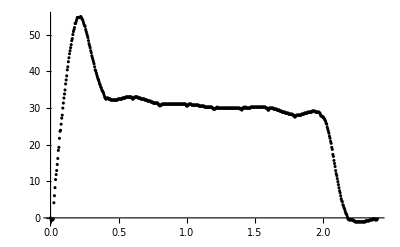

```mathematica
fitcurve=Fit[xy,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12x^13,x^14},x]
Show[ListPlot[xy,PlotStyle->Black],Plot[fitcurve,{x,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]]
```

```mathematica
fitcurve
```

0.707107 (1.15239 x-0.139656 y)+0.447214 x (0.523476 x+0.0287091 y)+0.242536 x^2 (0.0611491 x+0.142512 y)+0.124035 x^3 (-0.196556 x+0.202721 y)+0.0623783 x^4 (-0.328004 x+0.232545 y)+0.0312348 x^5 (-0.393731 x+0.247228 y)+0.0156231 x^6 (-0.42651 x+0.254493 y)